```mathematica
solF= NDSolve[{u''[t]== 1.3*(16.6-u'[t]), u[t /; t≤ 0] == 0, u'[t /; t≤ 0] == 0},u,{t,0 ,20}];

Evaluate[u'[8] /.solF][[1]]
```

16.5995

```mathematica
g[t_] :=(16 ⅇ^(-a t) (1-ⅇ^(a t)+a ⅇ^(a t) t))/a
g'[t]
```

16 a t-16 ⅇ^(-a t) (1-ⅇ^(a t)+a ⅇ^(a t) t)

```mathematica
Solve[{(100*1.03)/16-1==Exp[-1.03*t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.644}}

```mathematica
16*(Exp[-8*1.2]+1)
```

16.0011

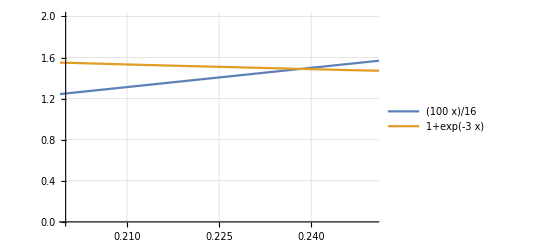

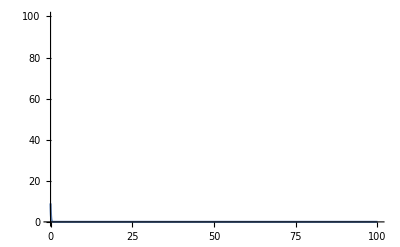

```mathematica
Plot[{100/16*x,1+Exp[-3*x]},{x,0,100}, PlotRange->{{0.2,0.25},{0,2}},PlotLegends->"Expressions",GridLines->Automatic]
```

```mathematica
sol=NDSolve[{u''[t]== Q[2000,u[t],u'[t]]* 1*(16.6-u'[t])+
1*QQ[2000,u[t],u'[t]]*(( (u'[t]^2*(-u'[t]+0)))/(2000-u[t])^2)
, u[t /; t≤ 0] == 0, u'[t /; t≤ 0] == 0},u,{t,0 ,tmax}];

Evaluate[u'[8] /.sol][[1]]
```

16.5944